```mathematica
A2:=f;
A22:=2 (f^2-f^3);
A4:=f^3;
A222:=5 f^3-12 f^4+7 f^5;
A24:=6 (f^4-f^5);
A6:=f^5;
A2222:=14 f^4+rest
```

```mathematica
Solve[{x+y+z+u+v==0,x/2+y/3+z/4+u/5+v/6==1/12,x+2y+3z+4u+5v==-1/3}]
```

{{x→2/3-(2 u)/5-v,y→-1+(9 u)/5+4 v,z→1/3-(12 u)/5-4 v}}

{16 f^5,-24 f^4,11 f^3,-(6 f^2)/L^2,(4 f)/L^2}

```mathematica
Z8:=S8;
Z26:=S26-Z8;
Z44:=S44-Z8;
Z224:=S224-Z44-2Z26-Z8;
Z2222:=S2222-6Z224-3Z44-4Z26-Z8;
```

```mathematica
MonomialList[105Z2222+210Z224+35Z44+28Z26+Z8]
```

{-420 S224,140 S44,448 S26,-272 S8,105 S2222}

```mathematica
trace2nterms:={(2f)/(1+x),Apart[((2 f^2-2 f^3) 4 (5+x))/((1+x) (2+x) (3+x))+(12 f^3)/((2+x) (3+x)),f],Apart[((5 f^3-12 f^4+7 f^5) 8 (x^2+15 x+74))/((1+x) (2+x) (3+x) (4+x) (5+x))+(6 (f^4-f^5) 24 (x+9))/((1+x) (3+x) (4+x) (5+x))+(f^5 120)/((3+x) (4+x) (5+x)),f],(14 f^4 16 (x^3+30 x^2+371 x+2118))/((1+x) (2+x) (3+x) (4+x) (5+x) (6+x) (7+x))}; trace2nterms
```

{(2 f)/(1+x),(4 f^3 (-7+x))/((1+x) (2+x) (3+x))+(8 f^2 (5+x))/((1+x) (2+x) (3+x)),(40 f^3 (74+15 x+x^2))/((1+x) (2+x) (3+x) (4+x) (5+x))+f^4 ((144 (9+x))/((1+x) (3+x) (4+x) (5+x))-(96 (74+15 x+x^2))/((1+x) (2+x) (3+x) (4+x) (5+x)))+f^5 (120/((3+x) (4+x) (5+x))-(144 (9+x))/((1+x) (3+x) (4+x) (5+x))+(56 (74+15 x+x^2))/((1+x) (2+x) (3+x) (4+x) (5+x))),(224 f^4 (2118+371 x+30 x^2+x^3))/((1+x) (2+x) (3+x) (4+x) (5+x) (6+x) (7+x))}

```mathematica
Factor[{40 (74+15 x+x^2),144(x+9)(x+2)-96 (74+15 x+x^2),56 (74+15 x+x^2)-144(x+9)(x+2)+120(x+1)(x+2)}]
```

{40 (74+15 x+x^2),48 (-94+3 x+x^2),32 (56-12 x+x^2)}

```mathematica
Factor[4/3(x^2+15x+74)+1/3(x-7)(5+x)(4+x)]
```

1/3 (156+17 x+6 x^2+x^3)

(156+17 x+6 x^2+x^3)/(3 (1+x) (2+x) (3+x) (4+x) (5+x))

```mathematica
monomials:=MonomialList[(2 f)/((1+x) 2)+1/12 (((2 f^2-2 f^3) 4 (5+x))/((1+x) (2+x) (3+x))+(12 f^3)/((2+x) (3+x)))+1/30 (((5 f^3-12 f^4+7 f^5) 8 (x^2+15 x+74))/((1+x) (2+x) (3+x) (4+x) (5+x))+(6 (f^4-f^5) 24 (x+9))/((1+x) (3+x) (4+x) (5+x))+(f^5 120)/((3+x) (4+x) (5+x)))+1/56 ((14 f^4 16 (x^3+30 x^2+371 x+2118))/((1+x) (2+x) (3+x) (4+x) (5+x) (6+x) (7+x))+rest),f,"NegativeLexicographic"]
```

```mathematica
TableForm[Table[Factor[monomials⟦n⟧],{n,2,Length[monomials]}]]
```

f/(1+x)
(2 f^2 (5+x))/(3 (1+x) (2+x) (3+x))
(f^3 (156+17 x+6 x^2+x^3))/(3 (1+x) (2+x) (3+x) (4+x) (5+x))
(4 f^4 (2694-337 x+124 x^2+37 x^3+2 x^4))/(5 (1+x) (2+x) (3+x) (4+x) (5+x) (6+x) (7+x))
(16 f^5 (56-12 x+x^2))/(15 (1+x) (2+x) (3+x) (4+x) (5+x))

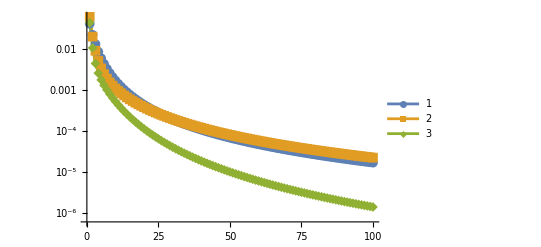

```mathematica
ListLogPlot[{Table[Abs[1/(2(1+x)^2)-(2 (5+x))/(3 (1+x) (2+x) (3+x))],{x,1,100}],Table[Abs[1/(12(1+x)^2)-(156+17 x+6 x^2+x^3)/(3 (1+x) (2+x) (3+x) (4+x) (5+x))],{x,1,100}],Table[Abs[1/(20(1+x)^3)-(4 (2694-337 x+124 x^2+37 x^3+2 x^4))/(5 (1+x) (2+x) (3+x) (4+x) (5+x) (6+x) (7+x))],{x,1,100}]},PlotLegends->Automatic,Joined->True,PlotMarkers->{Automatic,10}]
```

```mathematica
Apart[(4/5(2694-337 x+124 x^2+37 x^3+2 x^4))/((1+x) (2+x) (3+x) (4+x) (5+x) (6+x) (7+x))]
```

52/(15 (1+x))-24/(2+x)+332/(5 (3+x))-278/(3 (4+x))+342/(5 (5+x))-126/(5 (6+x))+18/(5 (7+x))

```mathematica
Apart[((156+17 x+6 x^2+x^3) 12)/(3 ((1+x) (2+x) (3+x) (4+x) (5+x)))]
```

24/(1+x)-92/(2+x)+132/(3+x)-80/(4+x)+16/(5+x)

```mathematica
Apart[(3*(5+x)*2/3)/((1+x) (2+x) (3+x))]
```

4/(1+x)-6/(2+x)+2/(3+x)

```mathematica
1/2 {28/15,-72/5,236/5,-230/3,318/5,-126/5,18/5} 15
```

```mathematica
coefffs:={{1},{4/3,-2,2/3},{2,-23/3,11,-20/3,4/3},{52/15,-24,332/5,-278/3,342/5,-126/5,18/5}}
```

```mathematica
Table[∑_(i=1)^Length[coefffs⟦j⟧] (coefffs⟦j⟧⟦i⟧)/(i+1)^j,{j,1,Length[coefffs]}]
```

{1/2,11/72,1307/14400,884785697/11854080000}

```mathematica
Bn[m_]:=Sum[coefffs[[m]][[k]]/(k+x),{k,1,2m-1}]
```

```mathematica
TableForm[Table[Apart[Bn[m]],{m,2,4}]]
```

4/(3 (1+x))-2/(2+x)+2/(3 (3+x))
2/(1+x)-23/(3 (2+x))+11/(3+x)-20/(3 (4+x))+4/(3 (5+x))
52/(15 (1+x))-24/(2+x)+332/(5 (3+x))-278/(3 (4+x))+342/(5 (5+x))-126/(5 (6+x))+18/(5 (7+x))

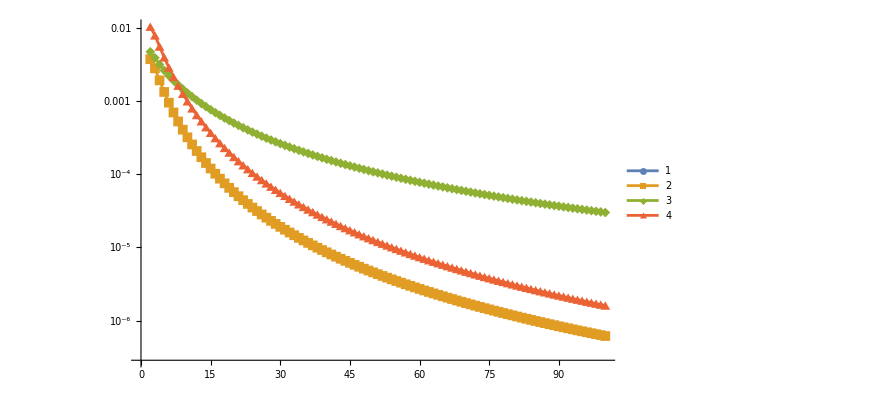

```mathematica
ListLogPlot[Table[Table[Abs[(2/(1+x))^m/(m(m+1))-Sum[coefffs[[m]][[k]]/(k+x),{k,1,2m-1}]],{x,1,100}],{m,1,4}],PlotLegends->Automatic,Joined->True,PlotMarkers->{Automatic,10}]
```

```mathematica
Factor[D[x/(1+x/k),{x,2}]]
```

-(2 k^2)/(k+x)^3